```mathematica
<<Histograms`
```

```mathematica
dataroot = "c:\\hannes\\skyline\\mathematica\\histo\\";
cor = Import[dataroot <> "c2d1e5.csv"];
```

```mathematica
Histogram3D[cor]
```

-Graphics3D-

```mathematica
d = 0.01;
corbins = BinCounts[cor, {0,1 +d , d}, {0,1 + d, d}];
```

```mathematica
arrayplot=ArrayPlot[corbins];
arrayplot
```

-Graphics-

```mathematica
Export["arrayplot.pdf", arrayplot, ImageSize]
```

arrayplot.pdf

```mathematica
ListPlot3D[corbins, InterpolationOrder -> 0,Mesh->None]
```

-Graphics3D-

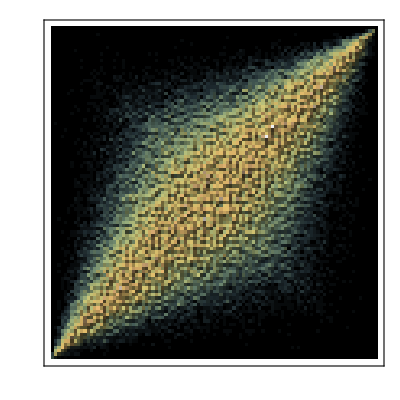

```mathematica
ReliefPlot[corbins, ColorFunction->"GreenBrownTerrain"]
```

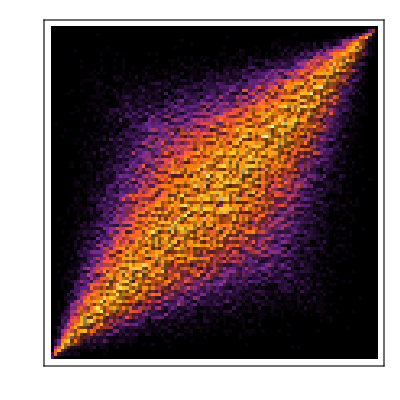

```mathematica
ReliefPlot[corbins, ColorFunction->"SunsetColors"]
```

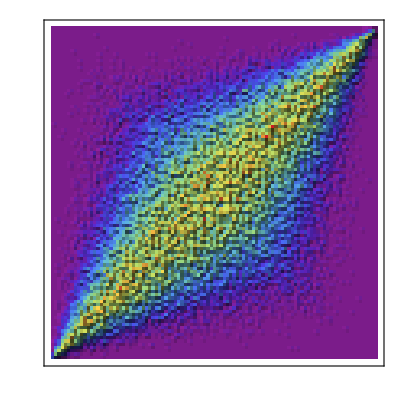

```mathematica
relplot = ReliefPlot[corbins, ColorFunction->"Rainbow"]
```

```mathematica
Export["relplot.pdf", relplot]
```

relplot.pdf

```mathematica
corint =ListInterpolation[corbins, {{0,1}, {0,1}}];
```

```mathematica
plot3d = Plot3D[corint[x,y], {x,0,1},{y,0,1}];
plot3d
```

-Graphics3D-

```mathematica
Export["interplot3d.pdf", plot3d]
```

interplot3d.pdf